```mathematica
(* Setup metric *)
```

```mathematica
Sigma=r^2+a^2*Cos[h]^2
Delta=r^2-2*r+a^2
(*Clear[Sigma,Delta]*)
gmetnagataki={{-1+2*r/Sigma,2*r/Sigma,0,-2*a*r*Sin[h]^2/Sigma},{2*r/Sigma,1+2*r/Sigma,0,-a*Sin[h]^2*(1+2*r/Sigma)},{0,0,Sigma,0},{-2*a*r*Sin[h]^2/Sigma,-a*Sin[h]^2*(1+2*r/Sigma),0,Sin[h]^2/Sigma*((r^2+a^2)^2-Delta*a^2*Sin[h]^2)}}
gmet={{-1+2*r/Sigma,2*r/Sigma,0,-2*a*r*Sin[h]^2/Sigma},{2*r/Sigma,1+2*r/Sigma,0,-a*Sin[h]^2*(1+2*r/Sigma)},{0,0,Sigma,0},{-2*a*r*Sin[h]^2/Sigma,-a*Sin[h]^2*(1+2*r/Sigma),0,Sin[h]^2*(Sigma+a^2*(1+2*r/Sigma)*Sin[h]^2)}}
MatrixForm[gmet]
```

r^2+a^2 Cos[h]^2

a^2-2 r+r^2

{{-1+(2 r)/(r^2+a^2 Cos[h]^2),(2 r)/(r^2+a^2 Cos[h]^2),0,-(2 a r Sin[h]^2)/(r^2+a^2 Cos[h]^2)},{(2 r)/(r^2+a^2 Cos[h]^2),1+(2 r)/(r^2+a^2 Cos[h]^2),0,-a (1+(2 r)/(r^2+a^2 Cos[h]^2)) Sin[h]^2},{0,0,r^2+a^2 Cos[h]^2,0},{-(2 a r Sin[h]^2)/(r^2+a^2 Cos[h]^2),-a (1+(2 r)/(r^2+a^2 Cos[h]^2)) Sin[h]^2,0,(Sin[h]^2 ((a^2+r^2)^2-a^2 (a^2-2 r+r^2) Sin[h]^2))/(r^2+a^2 Cos[h]^2)}}

{{-1+(2 r)/(r^2+a^2 Cos[h]^2),(2 r)/(r^2+a^2 Cos[h]^2),0,-(2 a r Sin[h]^2)/(r^2+a^2 Cos[h]^2)},{(2 r)/(r^2+a^2 Cos[h]^2),1+(2 r)/(r^2+a^2 Cos[h]^2),0,-a (1+(2 r)/(r^2+a^2 Cos[h]^2)) Sin[h]^2},{0,0,r^2+a^2 Cos[h]^2,0},{-(2 a r Sin[h]^2)/(r^2+a^2 Cos[h]^2),-a (1+(2 r)/(r^2+a^2 Cos[h]^2)) Sin[h]^2,0,Sin[h]^2 (r^2+a^2 Cos[h]^2+a^2 (1+(2 r)/(r^2+a^2 Cos[h]^2)) Sin[h]^2)}}

(-1+(2 r)/(r^2+a^2 Cos[h]^2) | (2 r)/(r^2+a^2 Cos[h]^2) | 0 | -(2 a r Sin[h]^2)/(r^2+a^2 Cos[h]^2)
(2 r)/(r^2+a^2 Cos[h]^2) | 1+(2 r)/(r^2+a^2 Cos[h]^2) | 0 | -a (1+(2 r)/(r^2+a^2 Cos[h]^2)) Sin[h]^2
0 | 0 | r^2+a^2 Cos[h]^2 | 0
-(2 a r Sin[h]^2)/(r^2+a^2 Cos[h]^2) | -a (1+(2 r)/(r^2+a^2 Cos[h]^2)) Sin[h]^2 | 0 | Sin[h]^2 (r^2+a^2 Cos[h]^2+a^2 (1+(2 r)/(r^2+a^2 Cos[h]^2)) Sin[h]^2))

```mathematica
(* compute gdet *)
```

```mathematica
FullSimplify[Det[gmet]]
FullSimplify[Det[gmetnagataki]]
mygdet=Abs[Sigma*Sin[h]]
thisgdet=Sqrt[-Det[gmet]]
nagatakigdet=Sqrt[-Det[gmet]]
FullSimplify[thisgdet-mygdet]
FullSimplify[nagatakigdet-mygdet]
```

-1/4 (a^2+2 r^2+a^2 Cos[2 h])^2 Sin[h]^2

-1/4 (a^2+2 r^2+a^2 Cos[2 h])^2 Sin[h]^2

Abs[(r^2+a^2 Cos[h]^2) Sin[h]]

√(r^4 Sin[h]^2+2 a^2 r^2 Cos[h]^2 Sin[h]^2+a^4 Cos[h]^4 Sin[h]^2)

√(r^4 Sin[h]^2+2 a^2 r^2 Cos[h]^2 Sin[h]^2+a^4 Cos[h]^4 Sin[h]^2)

-Abs[(r^2+a^2 Cos[h]^2) Sin[h]]+√((r^2+a^2 Cos[h]^2)^2 Sin[h]^2)

-Abs[(r^2+a^2 Cos[h]^2) Sin[h]]+√((r^2+a^2 Cos[h]^2)^2 Sin[h]^2)

```mathematica
(* Write down 2nd and 4th order solutions to flux *)
```

```mathematica
Li2[x_]:=-Integrate[Log[1-t*x]/t,{t,0,1}]
fofr=(Li2[2/r]-Log[1-2/r]*Log[r/2])*r^2*(2*r-3)/8+(1+3*r-6*r^2)/12*Log[r/2]+11/72+1/(3*r)+r/2-r^2/2
(*fofr=Fofr*)
(* Don't trust fofr vs. a*)
fofr=Limit[fofr,r->2]
Aphi0=C*(1-Cos[h])
Aphi2=C*fofr*Cos[h]*Sin[h]^2
Bphi1=-C/(4*r^2)*(1/2+2/r)
(* Set h1=h3=h5=b0=b2=0 since end up only being a^6 in energy flux and easier to deal with Nagataki to relevant desired order *)
h1=0
h3=0
h5=0
b0=0
b2=0
(*Aphi4=h1*Cos[h]+h3*Cos[h]^3+h5*Cos[h]^5*)
D1=0.01344; (* Aphi4 near pole *)
D2=0.05248; (* Aphi4 near equator *)
Clear[D1,D2];
l=2;Aphi4a=FullSimplify[Abs[Sin[h]]*LegendreP[l,1,Cos[h]],{h>0}];
l=4;Aphi4b=FullSimplify[Abs[Sin[h]]*LegendreP[l,1,Cos[h]],{h>0}];
Aphi4=C*(D1*Aphi4a+D2*Aphi4b);
Buphi3=g0+g2*Cos[2*h]
omega1=1/8
omega3=b0+b2*Cos[2*h]
gdet=mygdet
gdet=If[h>Pi/2,Evaluate[-Sigma*Sin[h]],Evaluate[Sigma*Sin[h]]]
gdet=Sigma*Sin[h] (* only for integration from 0 to pi/2 *)
rp=1+Sqrt[1-a^2]
OmegaH=a/(2*rp)

(* Nagataki form with expansion in a *)
omega=a*omega1+a^3*omega3
Aphi=Aphi0+a^2*Aphi2+a^4*Aphi4
Br=D[Aphi,h]/gdet
(* Enforce total flux to be constant *)
Print["Result of fixing flux"];
sols=Solve[fluxC==Integrate[Br*gdet,{h,0,Pi/2}],C]
Aphi=Aphi//.sols[[1]]
(* recompute Br *)
Print["Nagataki version of Br"];
Br=D[Aphi,h]/gdet
FE=(2*Br^2*omega*rp*(OmegaH-omega)*Sin[h]^2)//.{r->rp}
sFE=Series[FE,{a,0,4}]
(* do both hemispheres, so only integrate to pi/2 at most *)
dEdot=2*2*Pi*sFE*gdet//.{r->rp}
sdEdot=Series[dEdot,{a,0,4}]
(* Integrate up to finite angle: Ensure to compare factors of 2X correctly when only including one hemisophere *)
Edot=Integrate[sdEdot,{h,0,he}]
Edotlist=CoefficientList[Edot,a]
Edotfull=Edot//.{he->Pi/2}
powernagataki=C^2*(Pi/24)*a^2(1+1/45(56-3 Pi^2)a^2)
Print["If below is O[a^5], then I agree with Nagataki's paper shown result to a^4"];
FullSimplify[(Edotfull-powernagataki)//.{C->fluxC}]
Edotnagataki=Edot;
(* Integrate non-truncated Nagataki energy flux to get an idea of error introduced by higher order terms *)
Edotnagatakiextended=Integrate[dEdot,{h,0,he}]

(* omegah^2 form of expansion of A_\phi up to a^2 order *)
(* Choose omega to be omegaH/2 *)
myomega=OmegaH/2
myAphi=Aphi0+aphicoef*OmegaH^2*Aphi2+OmegaH^4*Aphi4
(* Enforce A_phi in omegah form to be same as A_\phi in $a$ form to a^2 order *)
lhs=CoefficientList[Normal[Series[Aphi//.{r->rp},{a,0,2}]],a]
rhs=CoefficientList[Normal[Series[myAphi//.{r->rp},{a,0,2}]],a]
Print["Below is result of coefficient assignment between Nagataki Aphi and omegah version of Aphi for a^2 term.  Has no angle dependence, so consistent without any trouble."];
sols=Solve[lhs[[3]]==rhs[[3]],aphicoef]
myAphi=myAphi//.sols[[1]]
myBr=D[myAphi,h]/gdet
(* Enforce total flux to be constant *)
Print["Result of fixing flux"];
sols=Solve[fluxC==Integrate[myBr*gdet,{h,0,Pi/2}],C]
myAphi=myAphi//.sols[[1]]
(* recompute Br *)
Print["omegah version of Br"];
myBr=D[myAphi,h]/gdet
(* Get final total energy flux with new Br *)
myFE=(2*myBr^2*myomega*rp*(OmegaH-myomega)*Sin[h]^2)//.{r->rp}
mysFE=Series[myFE,{a,0,4}]
(* Note that since myBr and myomega are consistent with Nagataki to lowest order, this myFE should be automatically consistent at the a^4 order, but still check *)
Print["If below ia O[a^5], then final myFE is consistent with Nagataki to a^4 order"];
FullSimplify[(sFE-mysFE)//.{fluxC->C},{-1≤a≤1}]
(* Get omegah version of energy flux on horizon without any order truncation *)
mydEdot=2*2*Pi*myFE*gdet//.{r->rp}
Clear[myEdot]
myEdot[a_,he_]:=NIntegrate[Evaluate[mydEdot//.{C->1,fluxC->1}],{h,0,he}]
```

11/72+1/(3 r)+r/2-r^2/2+1/12 (1+3 r-6 r^2) Log[r/2]+1/8 r^2 (-3+2 r) (-Log[1-2/r] Log[r/2]+PolyLog[2,2/r])

1/72 (-49+6 π^2)

C (1-Cos[h])

1/72 C (-49+6 π^2) Cos[h] Sin[h]^2

-(C (1/2+2/r))/(4 r^2)

0

0

0

«2 more identical outputs»

g0+g2 Cos[2 h]

1/8

0

Abs[(r^2+a^2 Cos[h]^2) Sin[h]]

If[h>π/2,(-r^2-a^2 Cos[h]^2) Sin[h],(r^2+a^2 Cos[h]^2) Sin[h]]

(r^2+a^2 Cos[h]^2) Sin[h]

1+√(1-a^2)

a/(2 (1+√(1-a^2)))

a/8

C (1-Cos[h])+1/72 a^2 C (-49+6 π^2) Cos[h] Sin[h]^2+a^4 C (-3 D1 Cos[h] Sin[h]^2-5/4 D2 Cos[h] (1+7 Cos[2 h]) Sin[h]^2)

1/(r^2+a^2 Cos[h]^2)Csc[h] (C Sin[h]+1/36 a^2 C (-49+6 π^2) Cos[h]^2 Sin[h]-1/72 a^2 C (-49+6 π^2) Sin[h]^3+a^4 C (-6 D1 Cos[h]^2 Sin[h]-5/2 D2 Cos[h]^2 (1+7 Cos[2 h]) Sin[h]+3 D1 Sin[h]^3+5/4 D2 (1+7 Cos[2 h]) Sin[h]^3+35/2 D2 Cos[h] Sin[h]^2 Sin[2 h]))

Result of fixing flux

{{C→fluxC}}

fluxC (1-Cos[h])+1/72 a^2 fluxC (-49+6 π^2) Cos[h] Sin[h]^2+a^4 fluxC (-3 D1 Cos[h] Sin[h]^2-5/4 D2 Cos[h] (1+7 Cos[2 h]) Sin[h]^2)

Nagataki version of Br

1/(r^2+a^2 Cos[h]^2)Csc[h] (fluxC Sin[h]+1/36 a^2 fluxC (-49+6 π^2) Cos[h]^2 Sin[h]-1/72 a^2 fluxC (-49+6 π^2) Sin[h]^3+a^4 fluxC (-6 D1 Cos[h]^2 Sin[h]-5/2 D2 Cos[h]^2 (1+7 Cos[2 h]) Sin[h]+3 D1 Sin[h]^3+5/4 D2 (1+7 Cos[2 h]) Sin[h]^3+35/2 D2 Cos[h] Sin[h]^2 Sin[2 h]))

(a (1+√(1-a^2)) (-a/8+a/(2 (1+√(1-a^2)))) (fluxC Sin[h]+1/36 a^2 fluxC (-49+6 π^2) Cos[h]^2 Sin[h]-1/72 a^2 fluxC (-49+6 π^2) Sin[h]^3+a^4 fluxC (-6 D1 Cos[h]^2 Sin[h]-5/2 D2 Cos[h]^2 (1+7 Cos[2 h]) Sin[h]+3 D1 Sin[h]^3+5/4 D2 (1+7 Cos[2 h]) Sin[h]^3+35/2 D2 Cos[h] Sin[h]^2 Sin[2 h]))^2)/(4 ((1+√(1-a^2))^2+a^2 Cos[h]^2)^2)

1/256 fluxC^2 Sin[h]^2 a^2+1/9216(45 fluxC^2 Sin[h]^2-116 fluxC^2 Cos[h]^2 Sin[h]^2+12 fluxC^2 π^2 Cos[h]^2 Sin[h]^2+49 fluxC^2 Sin[h]^4-6 fluxC^2 π^2 Sin[h]^4) a^4+O[a]^5

1/16 fluxC^2 π Sin[h]^3 a^2+1/576 (27 fluxC^2 π Sin[h]^3-107 fluxC^2 π Cos[h]^2 Sin[h]^3+12 fluxC^2 π^3 Cos[h]^2 Sin[h]^3+49 fluxC^2 π Sin[h]^5-6 fluxC^2 π^3 Sin[h]^5) a^4+O[a]^5

1/16 fluxC^2 π Sin[h]^3 a^2+1/576 (27 fluxC^2 π Sin[h]^3-107 fluxC^2 π Cos[h]^2 Sin[h]^3+12 fluxC^2 π^3 Cos[h]^2 Sin[h]^3+49 fluxC^2 π Sin[h]^5-6 fluxC^2 π^3 Sin[h]^5) a^4+O[a]^5

1/12 fluxC^2 π (2+Cos[he]) Sin[he/2]^4 a^2+1/34560 fluxC^2 π (1792-96 π^2+Cos[he] (-2942+201 π^2-4 (-346+33 π^2) Cos[2 he]+9 (-26+3 π^2) Cos[4 he])) a^4+O[a]^5

{0,0,1/12 fluxC^2 π (2+Cos[he]) Sin[he/2]^4,0,1/34560 fluxC^2 π (1792-96 π^2+Cos[he] (-2942+201 π^2-4 (-346+33 π^2) Cos[2 he]+9 (-26+3 π^2) Cos[4 he]))}

1/24 fluxC^2 π a^2+(fluxC^2 π (1792-96 π^2) a^4)/34560+O[a]^5

1/24 a^2 C^2 π (1+1/45 a^2 (56-3 π^2))

If below is O[a^5], then I agree with Nagataki's paper shown result to a^4

O[a]^5

1/12 fluxC^2 π (2+Cos[he]) Sin[he/2]^4 a^2+1/34560 fluxC^2 π (1792-96 π^2+Cos[he] (-2942+201 π^2-4 (-346+33 π^2) Cos[2 he]+9 (-26+3 π^2) Cos[4 he])) a^4+O[a]^5

a/(4 (1+√(1-a^2)))

C (1-Cos[h])+(a^2 aphicoef C (-49+6 π^2) Cos[h] Sin[h]^2)/(288 (1+√(1-a^2))^2)+(a^4 C (-3 D1 Cos[h] Sin[h]^2-5/4 D2 Cos[h] (1+7 Cos[2 h]) Sin[h]^2))/(16 (1+√(1-a^2))^4)

{fluxC-fluxC Cos[h],0,-49/72 fluxC Cos[h] Sin[h]^2+1/12 fluxC π^2 Cos[h] Sin[h]^2}

{C-C Cos[h],0,-(49 aphicoef C Cos[h] Sin[h]^2)/1152+1/192 aphicoef C π^2 Cos[h] Sin[h]^2}

Below is result of coefficient assignment between Nagataki Aphi and omegah version of Aphi for a^2 term.  Has no angle dependence, so consistent without any trouble.

{{aphicoef→(16 fluxC)/C}}

C (1-Cos[h])+(a^2 fluxC (-49+6 π^2) Cos[h] Sin[h]^2)/(18 (1+√(1-a^2))^2)+(a^4 C (-3 D1 Cos[h] Sin[h]^2-5/4 D2 Cos[h] (1+7 Cos[2 h]) Sin[h]^2))/(16 (1+√(1-a^2))^4)

1/(r^2+a^2 Cos[h]^2)Csc[h] (C Sin[h]+(a^2 fluxC (-49+6 π^2) Cos[h]^2 Sin[h])/(9 (1+√(1-a^2))^2)-(a^2 fluxC (-49+6 π^2) Sin[h]^3)/(18 (1+√(1-a^2))^2)+1/(16 (1+√(1-a^2))^4)a^4 C (-6 D1 Cos[h]^2 Sin[h]-5/2 D2 Cos[h]^2 (1+7 Cos[2 h]) Sin[h]+3 D1 Sin[h]^3+5/4 D2 (1+7 Cos[2 h]) Sin[h]^3+35/2 D2 Cos[h] Sin[h]^2 Sin[2 h]))

Result of fixing flux

{{C→fluxC}}

fluxC (1-Cos[h])+(a^2 fluxC (-49+6 π^2) Cos[h] Sin[h]^2)/(18 (1+√(1-a^2))^2)+(a^4 fluxC (-3 D1 Cos[h] Sin[h]^2-5/4 D2 Cos[h] (1+7 Cos[2 h]) Sin[h]^2))/(16 (1+√(1-a^2))^4)

omegah version of Br

1/(r^2+a^2 Cos[h]^2)Csc[h] (fluxC Sin[h]+(a^2 fluxC (-49+6 π^2) Cos[h]^2 Sin[h])/(9 (1+√(1-a^2))^2)-(a^2 fluxC (-49+6 π^2) Sin[h]^3)/(18 (1+√(1-a^2))^2)+1/(16 (1+√(1-a^2))^4)a^4 fluxC (-6 D1 Cos[h]^2 Sin[h]-5/2 D2 Cos[h]^2 (1+7 Cos[2 h]) Sin[h]+3 D1 Sin[h]^3+5/4 D2 (1+7 Cos[2 h]) Sin[h]^3+35/2 D2 Cos[h] Sin[h]^2 Sin[2 h]))

(a^2 (fluxC Sin[h]+(a^2 fluxC (-49+6 π^2) Cos[h]^2 Sin[h])/(9 (1+√(1-a^2))^2)-(a^2 fluxC (-49+6 π^2) Sin[h]^3)/(18 (1+√(1-a^2))^2)+1/(16 (1+√(1-a^2))^4)a^4 fluxC (-6 D1 Cos[h]^2 Sin[h]-5/2 D2 Cos[h]^2 (1+7 Cos[2 h]) Sin[h]+3 D1 Sin[h]^3+5/4 D2 (1+7 Cos[2 h]) Sin[h]^3+35/2 D2 Cos[h] Sin[h]^2 Sin[2 h]))^2)/(8 (1+√(1-a^2)) ((1+√(1-a^2))^2+a^2 Cos[h]^2)^2)

1/256 fluxC^2 Sin[h]^2 a^2+1/9216(45 fluxC^2 Sin[h]^2-116 fluxC^2 Cos[h]^2 Sin[h]^2+12 fluxC^2 π^2 Cos[h]^2 Sin[h]^2+49 fluxC^2 Sin[h]^4-6 fluxC^2 π^2 Sin[h]^4) a^4+O[a]^5

If below ia O[a^5], then final myFE is consistent with Nagataki to a^4 order

O[a]^5

(a^2 π Sin[h] (fluxC Sin[h]+(a^2 fluxC (-49+6 π^2) Cos[h]^2 Sin[h])/(9 (1+√(1-a^2))^2)-(a^2 fluxC (-49+6 π^2) Sin[h]^3)/(18 (1+√(1-a^2))^2)+1/(16 (1+√(1-a^2))^4)a^4 fluxC (-6 D1 Cos[h]^2 Sin[h]-5/2 D2 Cos[h]^2 (1+7 Cos[2 h]) Sin[h]+3 D1 Sin[h]^3+5/4 D2 (1+7 Cos[2 h]) Sin[h]^3+35/2 D2 Cos[h] Sin[h]^2 Sin[2 h]))^2)/(2 (1+√(1-a^2)) ((1+√(1-a^2))^2+a^2 Cos[h]^2))

```mathematica
eq=myBr//.{r->rp,a->0.9999,fluxC->1}
eq1=eq==3.0//.{h->0.000001}
eq2=eq==1.1//.{h->0.5}
Aphi4sols=Solve[{eq1,eq2},{D1,D2}][[1]]
```

1/(1.02848+0.9998 Cos[h]^2)Csc[h] (Sin[h]+1.10363 Cos[h]^2 Sin[h]-0.551815 Sin[h]^3+0.0590625 (-6 D1 Cos[h]^2 Sin[h]-5/2 D2 Cos[h]^2 (1+7 Cos[2 h]) Sin[h]+3 D1 Sin[h]^3+5/4 D2 (1+7 Cos[2 h]) Sin[h]^3+35/2 D2 Cos[h] Sin[h]^2 Sin[2 h]))

493028. (2.10363×10^-6+0.0590625 (-6.×10^-6 D1-0.00002 D2))==3.

1.15977 (0.826111+0.0590625 (-1.88479 D1-0.785195 D2))==1.1

{D1→0.348553,D2→-3.47491}

```mathematica
Limit[myAphi,h->Pi/2]
Limit[myAphi,h->0]
```

fluxC

0

{D1→-10,D2→-1.91}

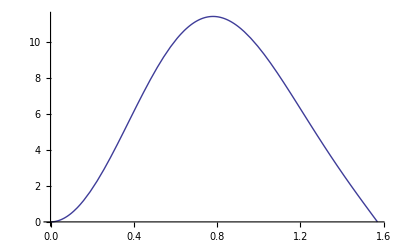

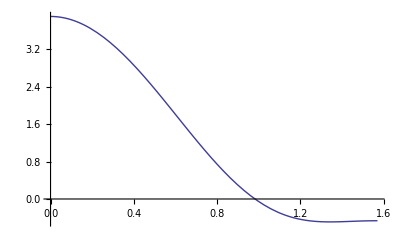

```mathematica
Aphi4sols={D1->-10,D2->-1.91}
otherconsts={a->0.9999,C->1,fluxC->1,r->rp};
Plot[Aphi4//.Aphi4sols//.otherconsts,{h,0,Pi/2}]
Plot[myBr//.Aphi4sols//.otherconsts,{h,0,Pi/2}]
```

0

{0.25}

{0.25}

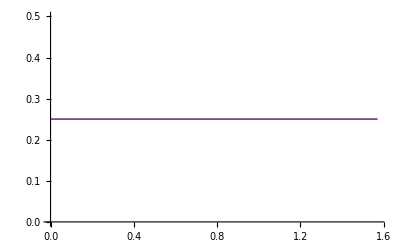

0.99

{0.812654}

{0.439856}

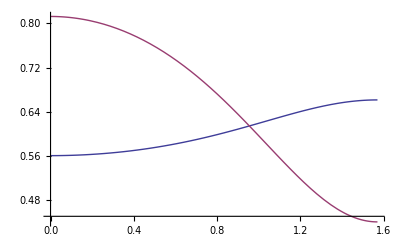

1.

{1.06765}

{0.432354}

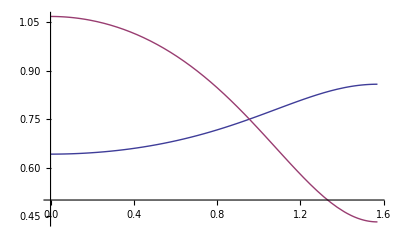

```mathematica
(* Check behavior of Br at a=0 and a=1 for Nagataki and omegah version of Br *)
mya=0
Brpolehor=N[Limit[myBr//.{r->rp,fluxC->1,a->mya},{h->0}]]
Brpoleeq=N[Limit[myBr//.{r->rp,fluxC->1,a->mya},{h->Pi/2}]]
toplot1=Br//.{r->rp,fluxC->1,a->mya};
toplot2=myBr//.{r->rp,fluxC->1,a->mya};
Plot[{toplot1,toplot2},{h,0,Pi/2}]

mya=0.99
Brpolehor=N[Limit[myBr//.{r->rp,fluxC->1,a->mya},{h->0}]]
Brpoleeq=N[Limit[myBr//.{r->rp,fluxC->1,a->mya},{h->Pi/2}]]
toplot1=Br//.{r->rp,fluxC->1,a->mya};
toplot2=myBr//.{r->rp,fluxC->1,a->mya};
Plot[{toplot1,toplot2},{h,0,Pi/2}]

mya=1.0
Brpolehor=N[Limit[myBr//.{r->rp,fluxC->1,a->mya},{h->0}]]
Brpoleeq=N[Limit[myBr//.{r->rp,fluxC->1,a->mya},{h->Pi/2}]]
toplot1=Br//.{r->rp,fluxC->1,a->mya};
toplot2=myBr//.{r->rp,fluxC->1,a->mya};
Plot[{toplot1,toplot2},{h,0,Pi/2}]
```

```mathematica
(* coefficient*)
pwr0anal=2Pi 0.0104167 (4OmH)^2  (* <- analytical expression for monopole BZ from BZ paper with a -> 4 OmH *)
coef=C*N[Normal[Series[Normal[Edotnagataki],{a,0,2}]]//.{he->Pi/2,fluxC->1}]/Normal[Series[(pwr0anal//.{OmH->a2OmH[a]}),{a,0,2}]//.{C->1}]
(*coef=C^2;*)
(* Numerical jet power from the simulation, nu = 0, for different spins *)
(* datax = a *)
(* datay = Power *)
datax={0.1,0.2,0.3,0.5,0.7,0.9,0.94,0.97,0.99,0.99769,0.999,0.999769,0.9999};
datay=coef*{0.00065565895056352,0.00266977190040052,0.00619285088032484,0.0191088989377022,0.0451582334935665,0.106693923473358,0.131530806422234,0.158286243677139,0.184633031487465,0.198393896222115,0.200842335820198,0.202311635017395,0.202582076191902};

a2OmH[a_]:=a/(2(1+Sqrt[1-a^2]));
OmH2a[OmH_]:=(4 OmH)/(1+4 OmH^2);
pwr0anal=coef*2Pi 0.0104167 (4OmH)^2  (* <- analytical expression for monopole BZ from BZ paper with a -> 4 OmH *)
pwrfullanal=coef*2Pi 0.0104167 (4OmH)^2(1+alpha OmH^2+beta OmH^4) (* <- analytical BZ plus high-order corrections *)
(* create a table for fitting data and fit the data *)
(* fit only deviations from the expected quadratic dependece on OmegaH: *)
varres=Table[a2OmH[datax[[i]]],{i,1,Length[datax]}]
fun1=Table[datay[[i]],{i,1,Length[datax]}]
fun2=Table[(pwr0anal/.{gamma->1,OmH->a2OmH[datax[[i]]]}),{i,1,Length[datax]}]
funres=fun1-fun2;
data=Table[{varres[[i]],funres[[i]]},{i,1,Length[datax]}];
Print["fit residual"];
res=Fit[data,{OmH^4,OmH^6},OmH]
(* find the corresponding best-fit alpha and beta coefficients of the expansion: *)
clist=CoefficientList[Collect[res-(pwrfullanal-pwr0anal),OmH],OmH]
bestfit=FullSimplify[Solve[clist==0,{alpha,beta}]][[1]]
(* expansion with the best-fit values of coefficients: *)
pwranal=pwrfullanal/.bestfit
sashafit=pwrfullanal//.{OmH->a2OmH[a]}//.bestfit//.{C->1}
```

1.0472 OmH^2

(0.1309 a^2 C)/(1.0472 a2OmH[0]^2+2.0944 a a2OmH[0] a2OmH'[0]+a^2 (1.0472 a2OmH'[0]^2+1.0472 a2OmH[0] a2OmH''[0]))

2.0944 C OmH^2

2.0944 C OmH^2 (1+alpha OmH^2+beta OmH^4)

{0.0250628,0.0505103,0.076768,0.133975,0.204184,0.313395,0.350439,0.390152,0.433804,0.467113,0.478123,0.489367,0.492978}

{0.00131131 C,0.00533953 C,0.0123857 C,0.0382177 C,0.0903162 C,0.213387 C,0.263061 C,0.316571 C,0.369265 C,0.396787 C,0.401683 C,0.404622 C,0.405163 C}

{0.00131558 C,0.0053434 C,0.012343 C,0.0375927 C,0.0873174 C,0.205703 C,0.257208 C,0.318806 C,0.394136 C,0.456986 C,0.478782 C,0.501565 C,0.508996 C}

fit residual

2.7025 C OmH^4-18.2968 C OmH^6

{0,0,0. C,0,2.7025 C-2.0944 alpha C,0,-18.2968 C-2.0944 beta C}

{alpha→1.29035,beta→-8.73607}

2.0944 C OmH^2 (1+1.29035 OmH^2-8.73607 OmH^4)

(0.523599 a^2 (1-(0.546004 a^4)/((1+√(1-a^2))^4)+(0.322587 a^2)/((1+√(1-a^2))^2)))/((1+√(1-a^2))^2)

(a^4 π (1792-96 π^2+Cos[he] (-2942+201 π^2-4 (-346+33 π^2) Cos[2 he]+9 (-26+3 π^2) Cos[4 he])))/34560+1/12 a^2 π (2+Cos[he]) Sin[he/2]^4

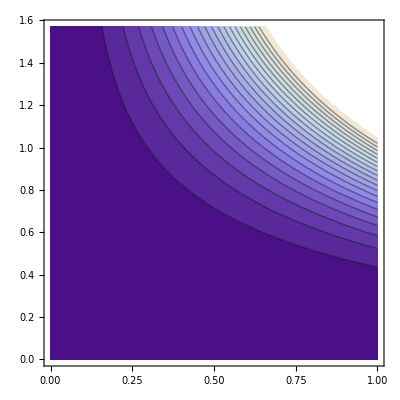

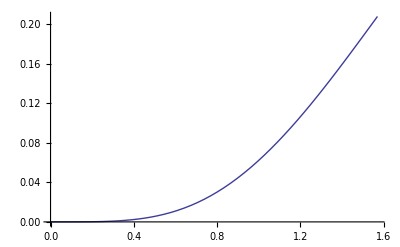

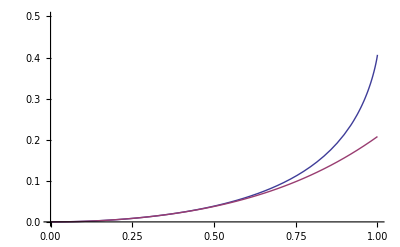

0.207669

0.406618

Ratio

1.95801

```mathematica
(* See Nagataki version with angle dependence *)
toplotfinalpowersasha=Normal[Edotnagataki]//.{C->1,fluxC->1}
ContourPlot[toplotfinalpowersasha,{a,0,1},{he,0,Pi/2},Contours->20]
Plot[(toplotfinalpowersasha//.{a->1}),{he,0,Pi/2}]
Plot[{sashafit,(toplotfinalpowersasha//.{he->Pi/2})},{a,0,1},PlotRange->{0,0.5}]
nag=N[Limit[toplotfinalpowersasha//.{a->1},he->Pi/2]]
sasha=N[Limit[sashafit//.{a->1},he->Pi/2]]
Print["Ratio"];
sasha/nag
```

```mathematica
mydEdot
```

(a^2 π Sin[h] (fluxC Sin[h]+(a^2 fluxC (-49+6 π^2) Cos[h]^2 Sin[h])/(9 (1+√(1-a^2))^2)-(a^2 fluxC (-49+6 π^2) Sin[h]^3)/(18 (1+√(1-a^2))^2))^2)/(2 (1+√(1-a^2)) ((1+√(1-a^2))^2+a^2 Cos[h]^2))

```mathematica
(* For now override since couldn't figure out how to setup assignment *)
myEdot[a_,he_]:=NIntegrate[((a^2 π Sin[h] (fluxC Sin[h]+(a^2 fluxC (-49+6 π^2) Cos[h]^2 Sin[h])/(9 (1+√(1-a^2))^2)-(a^2 fluxC (-49+6 π^2) Sin[h]^3)/(18 (1+√(1-a^2))^2))^2)/(2 (1+√(1-a^2)) ((1+√(1-a^2))^2+a^2 Cos[h]^2)))//.{C->1,fluxC->1},{h,0,he}]
```

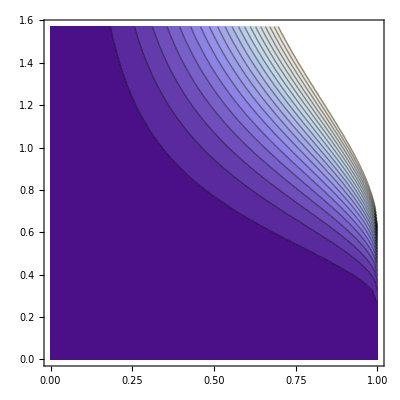

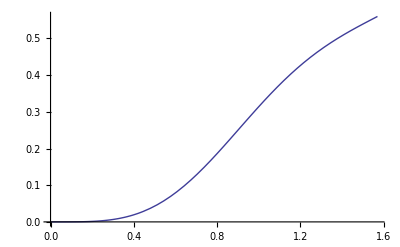

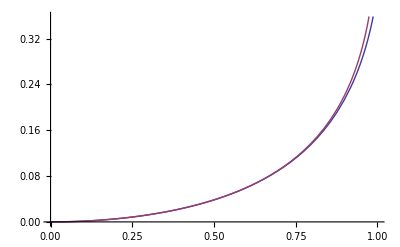

0.560009

0.560009

```mathematica
(* See omegah version with angle dependence *)
ContourPlot[myEdot[a,he],{a,0,1},{he,0,Pi/2},Contours->20]
Plot[myEdot[1,he],{he,0,Pi/2}]
Plot[{sashafit,myEdot[a,Pi/2-.0001]},{a,0,1}]
myEdot[1,Pi/2-0.00001]
N[%]
```

```mathematica
Series[OmegaH^2,{a,0,6}]
Series[2*OmegaH^2/rp,{a,0,6}]
Series[(1/2)*OmegaH^2*rp,{a,0,6}]
```

a^2/16+a^4/32+(5 a^6)/256+O[a]^7

a^2/16+(3 a^4)/64+(9 a^6)/256+O[a]^7

a^2/16+a^4/64+a^6/128+O[a]^7

```mathematica
datay//.{C->1}
rp=1+Sqrt[1-a^2];
pwranal//.{OmH->a/(2*rp),a->0.9999,C->1}
```

{0.0000858256,0.000349472,0.000810642,0.00250135,0.0059112,0.0139662,0.0172173,0.0207196,0.0241684,0.0259697,0.0262902,0.0264825,0.0265179}

0.0265717

(0.0342696 a^2 (1-(0.546004 a^4)/((1+√(1-a^2))^4)+(0.322587 a^2)/((1+√(1-a^2))^2)))/((1+√(1-a^2))^2)

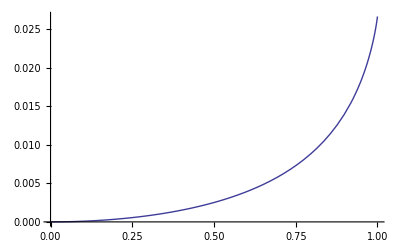

0

0.0266132

```mathematica
Plot[sashafit,{a,0,1}]
sashafit//.{a->0}
sashafit//.{a->1}
```